```mathematica
δa[r_]=(E^(-r^2/(2 a^2)))/((2π)^(3/2)a^3);α=1;u0=10^-10;a=1;αSch=2.;m=1;V[r_]=-1/#-(1.0415223038416566 ⅇ^(-0.9990999998788636#))/#&[r];VCou[r_]=-α/r;
Vs1[r_]=- α/r Erf[r/(√2 a)]+c1 a^2 δa[r]/.{c1->-44.29438139648679};
Vs2[r_]=- 1/# Erf[#/(√2 a)]+c2 a^2 δa[#]+d1 a^4 Laplacian[δa[#],{#,θ,ϕ},"Spherical"]&[r]/.{c2->-39.94772282822709,d1->3.265518446170086};
```

```mathematica
evShifted=Flatten@Import["C:\\Users\\ASUS\\Documents\\TestDATA_evShiftedHQ_NDSolve.dat"];
```

```mathematica
EigenEnergy[V_,αSch_,{min_,max_},{opt1___},{opt2___}]:=
Module[{sol,ef,evShifted,evnew,steps=∞,time1,time2},
PrintTemporary[V];
Module[{shift=10,d=1000,n=20,ev},{ev,ef}=NDEigensystem[{shift f[r]+V f[r]-1/αSch f''[r](*+NeumannValue[0,r==d]*),DirichletCondition[f[r]==0,True]},f[r],{r,0,d},n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.05}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}];
evShifted=ev-shift];
Print[evShifted];
sol=ParametricNDSolve[{V u[r]-1/αSch u''[r]==e u[r],u[max]==min,u'[max]==-min},u,{r,min,max},e,opt1,MaxSteps->Infinity];
evnew=e/.#&/@
Table[
PrintTemporary[n];FindRoot[u[e][min]==0/.sol,{e,0.99 SetPrecision[#[[n]],3],1.01 SetPrecision[#[[n]],3]}&[evShifted],opt2(*,StepMonitor:>PrintTemporary[e]*)],{n,20}]
]
```

```mathematica
evShifted=EigenEnergy[V[r],2m,{1.*10^-15,3000},{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}]
```

{-1.33732,-0.186434,-0.0710574,-0.0374072,-0.023051,-0.0156184,-0.0112778,-0.00852433,-0.00666881,-0.00535929,-0.0044008,-0.00367822,-0.00312003,-0.0026799,-0.00232673,-0.00203904,-0.00180159,-0.00160333,-0.00143608,-0.00129369}

ParametricNDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.04152 Power[«2»] Power[«2»]) u[r$16790]-u''[r$16790]/2==e$16789 u[r$16790],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

General::stop: Further output of FindRoot::brdig will be suppressed during this calculation.

{-1.33732035928243285421362210917,-0.186433943424584541601157040769,-0.0710574637876531605696874347145,-0.0374071688179521841396839447103,-0.0230509718270689921404347106972,-0.0156183900193265401748551373088,-0.0112777947775346078634093480762,-0.00852433316452207378188674048793,-0.00666880982256235846320125562769,-0.00535929279364405226881886381488,-0.00440080098984250795403943348203,-0.00367821996070517515892667693021,-0.00312003056979908688177687990896,-0.00267989789355987616067073310114,-0.00232673249010847154228712134351,-0.00203904412271491474165816403453,-0.00180159278404384743144571435647,-0.00160332767053397258106149462651,-0.00143607760576729575016509467183,-0.00129369534684217133425868439888}

```mathematica
energyVs2=EigenEnergy[Vs2[r],2m,{1.*10^-15,3000},{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}]
```

{-1.55584,-0.184813,-0.0710039,-0.0373997,-0.0230491,-0.0156178,-0.0112775,-0.00852421,-0.00666874,-0.00535926,-0.00440078,-0.00367821,-0.00312002,-0.00267989,-0.00232673,-0.00203904,-0.00180159,-0.00160333,-0.00143608,-0.00129369}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.53643 Power[«2»]+3.26552 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$54150]-u''[r$54150]/2==e$54149 u[r$54150],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

General::stop: Further output of FindRoot::brdig will be suppressed during this calculation.

{-1.55584171106920168119852757804,-0.184812889024214410806649524407,-0.0710038755178704016686884013386,-0.0373996869555343989709252798785,-0.023049112944692063495906182412,-0.015617756515474989476410087635,-0.0112775314310717020703481622059,-0.00852420772379227836737303471501,-0.00666874384520550239888757310241,-0.0053592553736366795161081941027,-0.00440077846881845844414747306724,-0.00367820574069967249817645208039,-0.0031200212286267581328870061422,-0.0026798915499048504848387769317,-0.00232672805832252119388856670794,-0.00203904095001752525746398130219,-0.00180159046383176967700015456942,-0.00160332594166236277436199440248,-0.00143607629594663152513709746502,-0.0012936943396727817190393087774}

```mathematica
Eigenfunsin[V_,ene_,rr_,{r1_,r2_},opt___]:=
Module[{efunction,amplitude},efunction=Flatten[NDSolve[{V f[r]-1/2m f''[r]==ene f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,r2},opt,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}],2];
amplitude=NIntegrate[f[r]^2/.#,{r,r2,r1}]^-0.5&/@efunction;
amplitude f[rr]/.efunction
]
```

```mathematica
AbsoluteTiming[efV=Module[{efunction=Range@20},
SetSharedVariable[efunction];
ParallelTable[
efunction[[n]]=First@Eigenfunsin[V[r],evShifted[[n]],r,{Which[n<14,2000,n<20,3000,n==20,4000],1.*10^-50},WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4,StartingStepSize->0.0001];efunction[[n]]=If[OddQ[n],efunction[[n]],-efunction[[n]]],{n,1,20}];
efunction
]];
```

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.04152 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-1.33732035928243285421362210917 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.04152 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.0374071688179521841396839447103 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.04152 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.0112777947775346078634093480762 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.04152 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.00535929279364405226881886381488 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.04152 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.00440080098984250795403943348203 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.04152 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.0230509718270689921404347106972 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.04152 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.00852433316452207378188674048793 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.04152 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.186433943424584541601157040769 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.04152 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.00367821996070517515892667693021 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.04152 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.0156183900193265401748551373088 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.04152 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.00666880982256235846320125562769 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.04152 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.0710574637876531605696874347145 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.04152 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.00312003056979908688177687990896 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.04152 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.00232673249010847154228712134351 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.04152 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.00180159278404384743144571435647 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.04152 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.00143607760576729575016509467183 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.04152 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.00267989789355987616067073310114 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.04152 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.00203904412271491474165816403453 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.04152 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.00160332767053397258106149462651 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.04152 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.00129369534684217133425868439888 f[r],f[4000]==1.×10^-50,f'[4000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

```mathematica
AbsoluteTiming[efVs2=Module[{efunction=Range@20},
SetSharedVariable[efunction];
ParallelTable[
efunction[[n]]=First@Eigenfunsin[Vs2[r],energyVs2[[n]],r,{Which[n<14,2000,n<20,3000,n==20,4000],1.*10^-50},WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4];efunction[[n]]=If[OddQ[n],efunction[[n]],-efunction[[n]]],{n,1,20}];
efunction
]]
```

NDSolve::precw: The precision of the differential equation ({{(-2.53643 Power[«2»]+3.26552 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-1.55584171106920168119852757804 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.53643 Power[«2»]+3.26552 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0373996869555343989709252798785 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.53643 Power[«2»]+3.26552 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0053592553736366795161081941027 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.53643 Power[«2»]+3.26552 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0112775314310717020703481622059 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.53643 Power[«2»]+3.26552 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00440077846881845844414747306724 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.53643 Power[«2»]+3.26552 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.023049112944692063495906182412 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.53643 Power[«2»]+3.26552 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00852420772379227836737303471501 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.53643 Power[«2»]+3.26552 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.184812889024214410806649524407 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.53643 Power[«2»]+3.26552 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00367820574069967249817645208039 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.53643 Power[«2»]+3.26552 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.015617756515474989476410087635 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.53643 Power[«2»]+3.26552 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00666874384520550239888757310241 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-2.53643 Power[«2»]+3.26552 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0710038755178704016686884013386 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-2.53643 Power[«2»]+3.26552 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0031200212286267581328870061422 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.53643 Power[«2»]+3.26552 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00232672805832252119388856670794 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.53643 Power[«2»]+3.26552 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00180159046383176967700015456942 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.53643 Power[«2»]+3.26552 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00143607629594663152513709746502 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.53643 Power[«2»]+3.26552 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0026798915499048504848387769317 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.53643 Power[«2»]+3.26552 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00203904095001752525746398130219 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.53643 Power[«2»]+3.26552 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00160332594166236277436199440248 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.53643 Power[«2»]+3.26552 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0012936943396727817190393087774 f[r],f[4000]==1.×10^-50,f'[4000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

{1470.67,{6.33092024525×10^-1484                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-8.51113405481×10^-475                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],2.27552×10^-271                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-1.82317×10^-179                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],1.51105×10^-126                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-6.49005×10^-92                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],2.35357×10^-67                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-5.91436×10^-49                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],1.32143×10^-34                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-4.51555×10^-23                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],1.40016×10^-13                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-0.0000127207                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],75.6493                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-2.32853×10^-22                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],6.65718×10^-15                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],-2.41906×10^-8                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],0.0158872                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],-2476.13                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],1.13454×10^8                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],-5.48908×10^-8                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 4000.0000000000000000000000000000000000000000000000}}, <>][r]}}

```mathematica
<<C:\\Users\\ASUS\\Documents\\TestDATA_δefVHQ.mx
<<C:\\Users\\ASUS\\Documents\\TestDATA_δefVs2HQ.mx
```

```mathematica
NIntegrate[D[efV[[1]],{r,2}]^2,{r,0,2000},{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30},Method->"GlobalAdaptive"]
 NIntegrate[D[efV[[1]],{r,2}]^2,{r,0,2000},{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30},Method->"Trapezoidal"]
 NIntegrate[D[efV[[1]],{r,2}]^2,{r,0,2000},{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30},Method->"AdaptiveMonteCarlo"]
```

NIntegrate::precw: The precision of the argument function (2.49684057453×10^-2743 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«3»,{{{{2,1},{2,1},«47»,{50,49},«55831»},{«1»}}}][r])^2) is less than WorkingPrecision (50.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {6.119082053817245906525543356318203531363531243959628944700809820382164082201630230118507291424741324×10^-50}. NIntegrate obtained 1.016532088399819703152625079520104513691025864832827411588168631271837445509132912776665321918751773×10^23 and 4.875613588279294617306614005493992382962946513984095973447100468989252488786766930111981628436642989×10^11 for the integral and error estimates.

1.0165320883998197031526250795201045136910258648328×10^23

NIntegrate::precw: The precision of the argument function (2.49684057453×10^-2743 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«3»,{{{{2,1},{2,1},«47»,{50,49},«55831»},{«1»}}}][r])^2) is less than WorkingPrecision (50.).

$Aborted

NIntegrate::precw: The precision of the argument function (2.49684057453×10^-2743 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«3»,{{{{2,1},{2,1},«47»,{50,49},«55831»},{«1»}}}][r])^2) is less than WorkingPrecision (50.).

4.0919846038394783577901480115580765559777229143395×10^-39

```mathematica
nRange=20;
```

```mathematica
Module[{efunction,n=20},
efunction=First@Module[{efunction1,amplitude,V=V[r],r1=2000,r2=1.*10^-20,ene=evShifted[[n]]},efunction1=Flatten[NDSolve[{V f[r]-1/2m f''[r]==ene f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,r2},WorkingPrecision->50,PrecisionGoal->20,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4,StartingStepSize->10^-6,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}],2];
amplitude=NIntegrate[f[r]^2/.#,{r,r2,r1}]^-0.5&/@efunction1;
amplitude f[r]/.efunction1
];efunction=If[OddQ[n],efunction,-efunction]]
```

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.04152 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.00129369534684217133425868439888 f[r],f[2000]==1.×10^-20,f'[2000]==-1.×10^-20},{},{},{},{}}) is less than WorkingPrecision (50.).

-4.26867                                                                              -21
InterpolatingFunction[{{9.999999999999999451532714542095716517295037027874 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r]

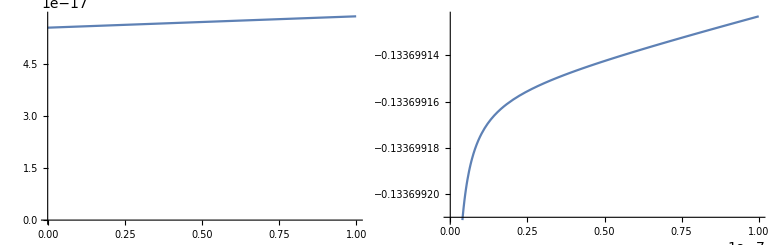

```mathematica
GraphicsGrid@{{Plot[#,{r,0,0.0000000000000001},ImageSize->Medium,AxesOrigin->{0,0}],Plot[Evaluate@D[#,{r,2}],{r,0,0.0000001},ImageSize->Medium]}}&[%48]
```

```mathematica
NIntegrate[D[efV[[#]],{r,2}]^2,{r,10^-20,2000},MaxRecursion->20,WorkingPrecision->50,PrecisionGoal->15]&/@{20}
```

NIntegrate::precw: The precision of the argument function (3.01244×10^-15 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,4000.}},«3»,{{{{2,1},{2,1},{3,2},{4,3},«44»,{49,48},{50,49},«11734»},«1»}}]«1»«1»])^2) is less than WorkingPrecision (50.).

{0.0035168904999131197696890845930440324974732164291244}

```mathematica
NIntegrate[D[efVs2[[#]],{r,2}]^2,{r,10^-25,2000},MaxRecursion->20,WorkingPrecision->50,PrecisionGoal->15]&/@{20}
```

NIntegrate::precw: The precision of the argument function (3.013×10^-15 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,4000.}},«3»,{{{{1},{1},{2},{3},{4},«41»,{46},{47},{48},{49},«11225»},«1»}}]«1»«1»])^2) is less than WorkingPrecision (50.).

{0.0012490194222614775190340223872311974292750122206061}

```mathematica
NIntegrate[D[efV[[#]],{r,2}]^2,{r,10^-20,2000},WorkingPrecision->30,MaxRecursion->10]&/@{19}
```

NIntegrate::precw: The precision of the argument function (1.28695×10^16 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,3000.}},«3»,{{{{2,1},{2,1},{3,2},«45»,{49,48},{50,49},«10612»},{«1»}}}][r])^2) is less than WorkingPrecision (30.).

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in r near {r} = {9.7258929935875821318963315950422998938141920818532842183489151086874907013655766×10^-17}. NIntegrate obtained 0.0041119081159898495435688505989268940692218654143341122945196688536567972162757348 and 4.1126584700249767151189249828579648785358449850190854905280350310334958054511098×10^-14 for the integral and error estimates.

{0.00411190811598984954356885059893}

```mathematica
REAL=NIntegrate[D[efV[[#]],{r,2}]^2,{r,0,2000},{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@Range@nRange;
N[%,6]
```

NIntegrate::precw: The precision of the argument function (2.49684057453×10^-2743 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«3»,{{{{2,1},{2,1},«47»,{50,49},«55831»},{«1»}}}][r])^2) is less than WorkingPrecision (50.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {6.119082053817245906525543356318203531363531243959628944700809820382164082201630230118507291424741324×10^-50}. NIntegrate obtained 1.016532088399819703152625079520104513691025864832827411588168631271837445509132912776665321918751773×10^23 and 4.875613588279294617306614005493992382962946513984095973447100468989252488786766930111981628436642989×10^11 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (1.61258374929×10^-953 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«3»,{{{{2,1},{2,1},«48»,«21087»},{«1»}}}]«1»«1»])^2) is less than WorkingPrecision (50.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {4.120892116289494056515341580009911447648234085524274816051798291309555157962950519352640668989941161×10^-50}. NIntegrate obtained 2.233664249531966017948466521140261473509789114701055698545361553785935050339489171748764235772331606×10^21 and 1.605941550487200508191635743482848607945813060616467148401185630218567846539283939127542656013664112×10^10 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (2.93346661229202×10^-542 («1»)^2) is less than WorkingPrecision (50.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {1.13047760538350879773228834225809715156981878821457083186386001602596433020274118615141596562324041×10^-49}. NIntegrate obtained 1.983563915089790045705366433119168699960163872513193978423436127718753037991571611549488635448450906×10^21 and 9.46112446775116671345580982964446596396001686676023288414406682820747253576094605749399079430271858×10^9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{1.01653×10^23,2.23366×10^21,1.98356×10^21,1.49199×10^20,1.20615×10^20,8.22732×10^20,2.40105×10^20,1.23455×10^20,9.21104×10^19,4.25102×10^19,2.46606×10^17,1.11937×10^19,2.6459×10^19,2.10889×10^18,1.43967×10^19,2.29878×10^18,2.6076×10^18,9.36252×10^17,2.58049×10^20,5.45308×10^18}

```mathematica
REF=REAL[[#]]&/@{10,15,20}
```

```mathematica
FALSE=NIntegrate[D[efVs2[[#]],{r,2}]^2,{r,0,2000},{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@Range@nRange;
N[%,6]
Abs@((REAL-FALSE)/REAL);
N[%,6]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.390162817166083110742177717868045501522678077610331222086970598643766457023111990453105165264494789 and 0.00009318058975739532885974257458735101285534270299034558245057898625762689075024696111033393628347551661 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.804673706092641070824791037528791708786011502034883000897617855289241310671958684372056406595798846 and 0.00003166525569617745446782981765016946254513427199870742607520883148545846902578524935674203476291123062 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.45918158548463745424659119589758562706718845870688775021904349749603028948017500444396012247019068 and 8.983939340099645512156358130543338990793133023411042290711278842405894418513687133710099766749343988×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{6.39016,1.80467,0.459182,0.181115,0.0892336,0.0503636,0.0311615,0.0206038,0.0143248,0.0103588,0.00773158,0.00592277,0.00463692,0.00369791,0.00299626,0.00246146,0.00204673,0.00172016,0.00145962,0.00278627}

{0.914872,0.694022,0.668193,0.660539,0.656377,0.653711,0.651849,0.650473,0.649413,0.648572,0.647888,0.64732,0.646842,0.646433,0.64608,0.645772,0.6455,0.64526,0.645029,0.446837}

```mathematica
inte1=Table[NIntegrate[(D[efVs2[[n]],{r,2}]^2),{r,0,2000},{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}],{n,1,20}];
inte2=Table[NIntegrate[efVs2[[n]]^2 δa[r],{r,0,2000},{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}],{n,1,20}];
inte3=Table[NIntegrate[efVs2[[n]]^2 D[δa[r],{r,2}],{r,0,2000},{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}],{n,1,20}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.390162817166083110742177717868045501522678077610331222086970598643766457023111990453105165264494789 and 0.00009318058975739532885974257458735101285534270299034558245057898625762689075024696111033393628347551661 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.804673706092641070824791037528791708786011502034883000897617855289241310671958684372056406595798846 and 0.00003166525569617745446782981765016946254513427199870742607520883148545846902578524935674203476291123062 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.45918158548463745424659119589758562706718845870688775021904349749603028948017500444396012247019068 and 8.983939340099645512156358130543338990793133023411042290711278842405894418513687133710099766749343988×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.03821994001544543894629564211239529533181876717084749624559979019422049380871139858439047001484064582 and 3.385150683853061054798669641802055824805734990827398522227922161326481197667325051308333494546240196×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00324008981456391683306314605305908753731755273394098994717277001241510283344810448354657589177778361 and 1.162573958757810282556652377509572238005177956177396987715010183217268521473323108128231425926293327×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000721537762420622426691812742755004090594313981791498109654635356834669059911641015995659622746510986 and 2.82909190158464904017834805310360386515483674591231848539461034672936272105389213473465515268591428×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

```mathematica
p4Ture[n_,b_][Z_,γ_,η_]:=Z inte1+γ/a inte2+η a inte3
```

```mathematica
RES=FindRoot[Evaluate@Thread[(p4Ture[#,2000][Z,γ,η]&/@{10,15,20})==REF](*/.Z->1*),{{Z,1.1,1.12},{γ,0,100},{η,100,-2}},WorkingPrecision->50,AccuracyGoal->6,PrecisionGoal->6]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.002461460116588555189385075433761026165284667233293829537617743201403816153138988575036624992613794694 and 4.817198128533707281802689557708705574702212002044683269690514122466254682031574139041305712365413007×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.388746212262176911689948358332735330446986433023158742798514611050647487789720229327801459266635598×10^-6 and 1.628619704204227175570271036186820914263804111415270231159873711193061806580639712961218773727950553×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.451720926163316825652779161657839028757917496150434650853254647437664848660113023744766635980003029×10^-6 and 3.432715270024195764346826100683067325912100395230017771183390190643197832420772382716321461342135196×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{Z→0.98882924043819329142242166456815359576467264085887,γ→1963.2131603181007310342597160601761534052982794961,η→-872.03953484540460044012833805538891104421101232679}

```mathematica
p4=p4Ture[#,2000][Z,γ,η,{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@Range@nRange/.RES;
N[%,6]
Abs[(p4-REAL)/REAL];
N[%,6]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.390162817166083110742177717868045501522678077610331222086970598643766457023111990453105165264494789 and 0.00009318058975739532885974257458735101285534270299034558245057898625762689075024696111033393628347551661 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.03821994001544543894629564211239529533181876717084749624559979019422049380871139858439047001484064582 and 3.385150683853061054798669641802055824805734990827398522227922161326481197667325051308333494546240196×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.006439692856478978773897744889573675887707993597983868171907767303889962679720287506307917533795964429 and 6.500416939576901683435807907570685834577292737718235658002729639679645134452441128739027625240735712×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{86.9683,5.62288,1.37744,0.532836,0.259546,0.1454,0.0894933,0.0589431,0.0408575,0.0294754,0.0219574,0.0167935,0.0131298,0.0104589,0.00846592,0.0069488,0.00577356,0.00484908,0.00411197,0.00503698}

{0.158572,0.0466549,0.0046522,0.00131318,0.000534049,0.000259682,0.000139205,0.0000789185,0.0000458985,0.0000266682,0.000015542,8.55158×10^-6,4.3692×10^-6,1.9922×10^-6,6.65066×10^-7,0.,1.21127×10^-7,0.,9.25972×10^-6,0.}